```mathematica
Apr 25,2018
```

```mathematica
(* General spherical rotations. Note the branch cut in ArcTan *)
NewArcTan[X_,Y_,phi_]:=Piecewise[{{ArcTan[X,Y]+2π,phi>π},{ArcTan[X,Y],phi≤π}}];   (* ,{0,X==0&&Y==0} *)
rotateθ[inc_]:=ArcCos[Cos[θ]Cos[inc]-Sin[θ]Cos[ϕ]Sin[inc]]; (*note: for ϕ=0, θ2 is just θ+ι cause cos(a+b)=cosacosb-sinasinb*)
rotateϕ[inc_]:= NewArcTan[(Sin[θ]Cos[ϕ]Cos[inc]+Cos[θ]Sin[inc]),(Sin[θ]Sin[ϕ]),ϕ];
```

```mathematica
(* Global Variables: 
 • inclination
• Rstar
• Ω
• M
• alpha, beta, α0
  • B1
  • Λ
  • fourcurrent, surfacecurrent, Jsquared 
*)
```

```mathematica
InitializeStar[inclangle_,GRon_]:=
Module[{μ,Ωz,θprime,ϕprime,II,MOI,f,Jt,Jr,Jθ,Jϕ},
(* Use dimensionless parameters?? *)
inclination = inclangle;
Rstar = 1; Ω = 0.1; μ=1; ϵ=Rstar*Ω; (*ϵ=0.1*) Compactness = 2M/Rstar; (*C=0.5*)
M = If[GRon,0.25,0];
II= If[GRon,2/5,0];  (* w/0 GR effects means C=I=0 *)
MOI=II*M*Rstar^2;

Ωz =(2*MOI)/r^3 Ω; (*frame-dragging frequency*)
f = 1-(2M)/r; 
θprime = rotateθ[inclination];
ϕprime=rotateϕ[inclination];

alpha=If[GRon, -3/2((3+2Log[f]-4f+f^2)/(1-f)^3)μ/r(Sin[θprime])^2,μ/r(Sin[θprime])^2];  (* NOTE: this alpha is only for the dipole! *)
beta= ϕprime;  (* Euler potentials in the far region of a dipole *)
α0=√(3/2)μ*Ω(1+1/5(Sin[inclangle])^2);  (* cut-off angle, beyond which there can be no spacelike current *)

(*magnorth = {θ->inclination,ϕ->0,r->Rstar};  (* NOTE: PROBLEM with ArcTan[0/0] at θ=0 ... *)
Bpole = Norm[Cross[Grad[alpha,{r,θ,ϕ},"Spherical"],Grad[beta,{r,θ,ϕ},"Spherical"]] /. magnorth];
*)(*Bpole = 2μ/Rstar^3;*)

B1=If[GRon,(1/2)(( -3/2((3+2Log[f]-4f+f^2)/(1-f)^3)μ/r)/.r->Rstar)/Rstar^2,(1/2)μ/Rstar^3] ;  (* α = Rstar^2∑_(l=1)^∞ Subscript[B, l] Subscript[Θ, l](θ). For the pure dipole, Subscript[Θ, 1]=Sin^2[θ] *)
 
Λ[α_,β_]:=Piecewise[{{-2Ω(BesselJ[0,2ArcSin[√(α/α0)]]Cos[inclination] - BesselJ[1,2ArcSin[√(α/α0)]]Cos[β]*Sin[inclination]),α≤α0},{0,α>α0}}];  (*a close numerical fit, derived in appendix B of the paper*)

(* The four-current in orthonormal co-ordinates: *)
Jt[α_,β_]:= (√(1-(2M)/r)) (Ω-Ωz)/(r(r-2M))( D[α, θ] D[D[β, ϕ], θ] - D[β, θ] D[D[α, ϕ], θ]  + (r(r-2M))(D[α, r] D[D[β, ϕ], r] - D[β, r] D[D[α, ϕ], r]) 
- D[α, ϕ]((1-(2M)/r)D[(r^2 D[β, r]), r]+D[(Sin[θ]D[β, θ]), θ]/Sin[θ]) + D[β, ϕ]((1-(2M)/r)D[(r^2 D[α, r]), r]+D[(Sin[θ]D[α, θ]), θ]/Sin[θ])); (* Jt = charge density ρ *) 
Jr[α_,β_]:= Λ[α,β]/(√(r(r-2M))(r*Sin[θ]))(D[α, θ] D[β, ϕ] - D[β, θ] D[α, ϕ]);
Jθ[α_,β_]:= Λ[α,β]/(r*Sin[θ])(D[α, ϕ] D[β, r] - D[α, r] D[β, ϕ]);
Jϕ[α_,β_]:= Λ[α,β]/r(D[α, r] D[β, θ] - D[α, θ] D[β, r]);

fourcurrentJ[α_,β_]:= {Jt[α,β],Jr[α,β],Jθ[α,β],Jϕ[α,β]};
surfacecurrent = Evaluate[fourcurrentJ[alpha,beta] /.{r->Rstar}];
Jsquared = (-surfacecurrent[[1]]^2+surfacecurrent[[2]]^2+surfacecurrent[[3]]^2+surfacecurrent[[4]]^2);
]
```

```mathematica
(* ------------------------------------------------------------------------ *)
```

```mathematica
(* Plot the polar cap *)
(*PlotCap[signonly_,pps_,colorrange_]:=*)
PlotCap[]:=
Module[{x,y,θprime,ϕprime,f,JJ,αmess},
θθ=rotateθ[-inclination]/.{θ->θprime,ϕ->ϕprime}; (* inverse transformation is just minus the original *)
ϕϕ=rotateϕ[-inclination]/.{θ->θprime,ϕ->ϕprime};
rotmap = {θ->θθ,ϕ->ϕϕ};
patchmap ={θprime->ArcSin[√(x^2+y^2)/Rstar],ϕprime-> ArcTan[x,y]};  (*transform to cartesian coordinates to plot the patch*)
patchsize = 0.4;
f = 1-(2M)/r; 
If[M==0,αmess=1,αmess=-3/2((3+2Log[f]-4f+f^2)/(1-f)^3)/.r->Rstar]; (* if we ignore GR, the limit of this expression is (-2/3) *)
θmax = ArcSin[((√(3/2)(1+(Sin[inclination]^2/5))ϵ)/αmess )^(1/2)];(* the angle at which α=α0 *)

(*JJ=((Jsquared*Rstar^2)/(ϵ^2*B1^2) );*)
DensityPlot[(((Jsquared*Rstar^2)/(ϵ^2*B1^2) )/.rotmap)/.patchmap,{x,-patchsize,patchsize},{y,-patchsize,patchsize},RegionFunction->Function[{x,y},ArcSin[√(x^2+y^2)/Rstar]<θmax],ColorFunction->ColorData["Temperature"],PlotLegends->Automatic,PlotPoints-> 40,PlotRange->All]

(*If[signonly,
CapPlot=DensityPlot[ Sign[(JJ/.rotmap)/.patchmap],{x,-patchsize,patchsize},{y,-patchsize,patchsize},RegionFunction->Function[{x,y},0<ArcSin[√(x^2+y^2)/Rstar ]<θmax],ColorFunction->"BlueGreenYellow",PlotPoints-> pps,Frame->False, PlotLabel->i==inclination],
CapPlot=DensityPlot[ (JJ/.rotmap)/.patchmap,{x,-patchsize,patchsize},{y,-patchsize,patchsize},RegionFunction->Function[{x,y},ArcSin[√(x^2+y^2)/Rstar ]<θmax],ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-colorrange,colorrange}]]&),ColorFunctionScaling->False,PlotLegends->Automatic,PlotPoints-> pps]  ]*)
]
```

```mathematica
(* ----------------------------------------------------------------------- *)
```

```mathematica
RunSim[i_,TF_]:= (InitializeStar[i,TF];PlotCap[]);
```

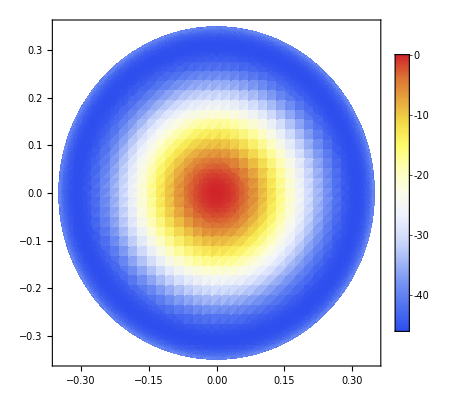
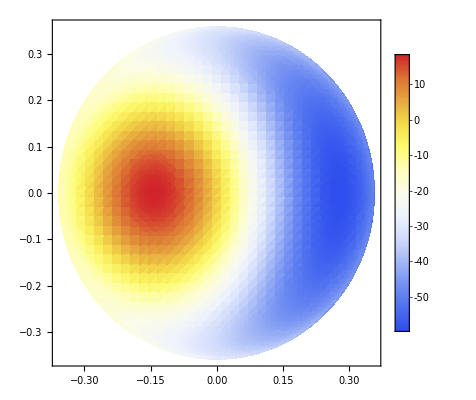
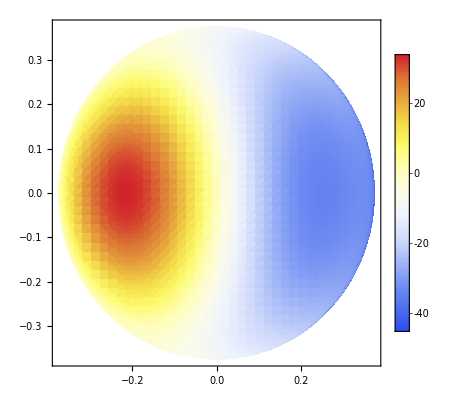
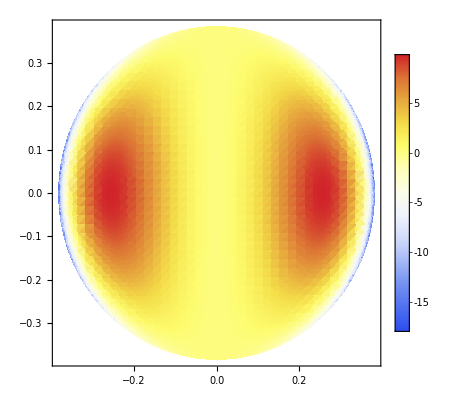

```mathematica
Table[RunSim[ii,False],{ii,0,Pi/2,Pi/6}]
```

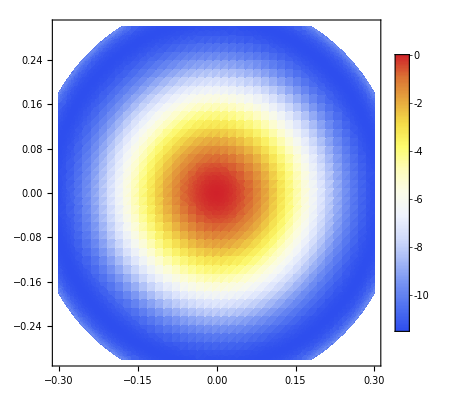
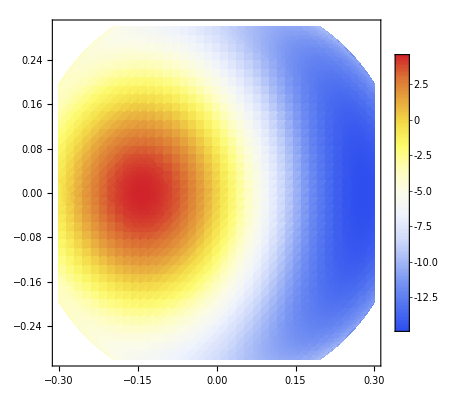
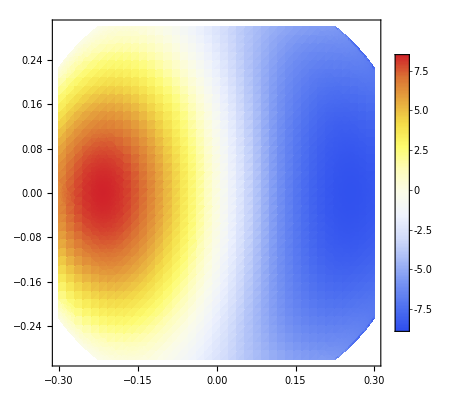
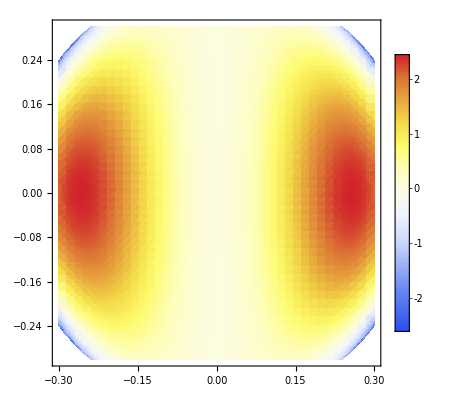

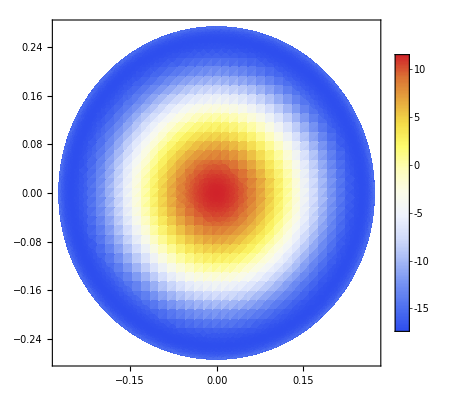
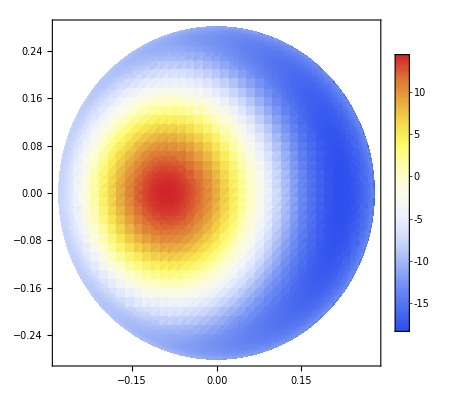
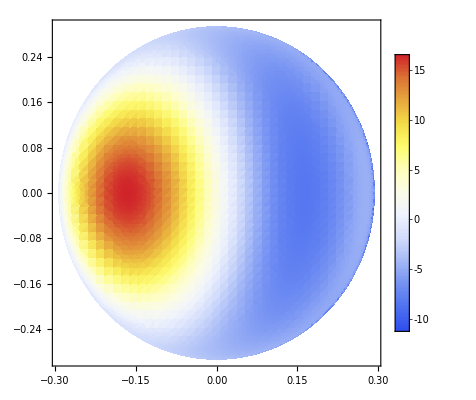
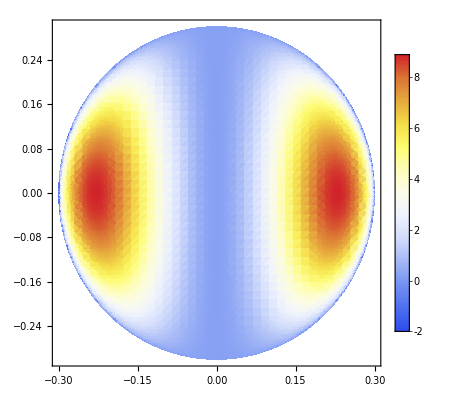

```mathematica
Table[RunSim[ii,True],{ii,0,Pi/2,Pi/6}]
```

```mathematica
RunSim[Pi/2,False]
```

-Graphics-

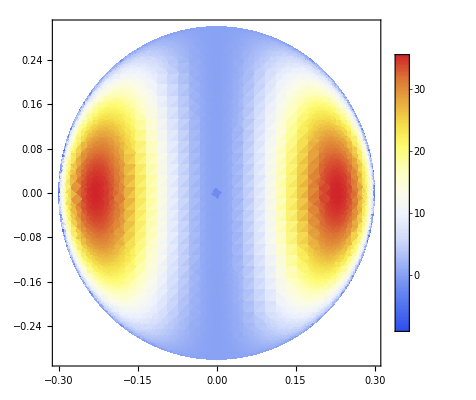

```mathematica
RunSim[Pi/2,True]
```

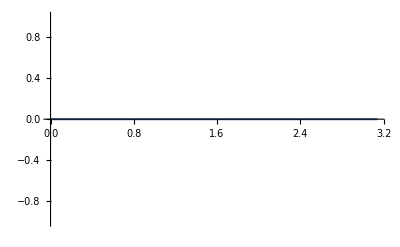

```mathematica
Plot[Jsquared/.{ϕ->0.1},{θ,0,Pi},PlotRange->All]
```

```mathematica
makesignplot[ii_,pp_]:=(InitializeStar[ii,True];PlotCap[True,pp,0]);
plotlist = {};
```

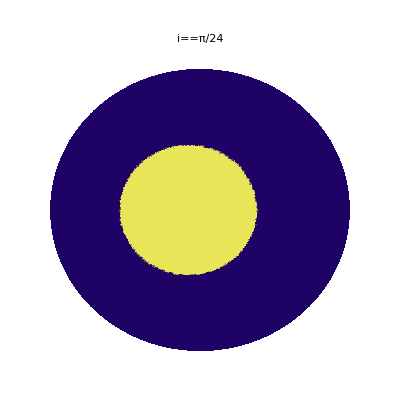
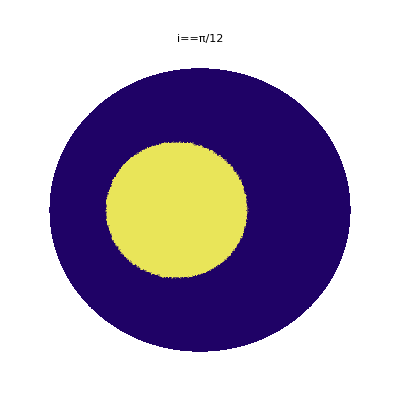
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[plotlist ,makesignplot[12Pi/24,120]]
```

```mathematica
Export["sign_plot_table.png",
GraphicsGrid[{
Table[plotlist[[k]],{k,1,4}],
Table[plotlist[[k]],{k,5,8}],
Table[plotlist[[k]],{k,9,12}]
}],ImageResolution->1000
]
```

sign_plot_table.png

```mathematica
Export["sign_plot_table.png",GraphicsGrid[
{Table[makesignplot[angle,150],{angle,Pi/24,4Pi/24,Pi/24}],
Table[makesignplot[angle,150],{angle,5Pi/24,8Pi/24,Pi/24}],
Table[makesignplot[angle,150],{angle,8Pi/24,12Pi/24,Pi/24}]
}],ImageResolution->1000
]
```

$Aborted

```mathematica
plotlist
```

{-Graphics-}

```mathematica
GraphicsRow[{dostuff[0,12],dostuff[Pi/6,15],dostuff[Pi/3,8],dostuff[Pi/2,5]}]
```

-Graphics-

```mathematica
InitializeStar[Pi/3,True];PlotCap[False,40,20]
```

-Graphics-

```mathematica
PlotLambda[ang_]:=(InitializeStar[ang,False];
Fig4=Plot[Evaluate[(Λ[alpha,beta]/Ω) /. {r->Rstar,ϕ->0}] ,{θ,ang-π/2,ang+π/2}, PlotRange->All, AxesLabel->{"θ","Λ/Ω"}])
```

```mathematica
Table[PlotLambda[newinc],{newinc,{0,Pi/6,Pi/3,Pi/2}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[surfacecurrent[[1]]/.{ϕ->0},{θ,0,Pi},PlotRange->All]
```

-Graphics-

```mathematica
Limit[ surfacecurrent[[1]]/.{ϕ->1},θ->0]
```

8.26854

```mathematica
Limit[-3/2((3+2Log[f]-4f+f^2)/(1-f)^3),f->1]
```

1

```mathematica
DensityPlot[ Sign[Sin[x]],{x,-1,1},{y,-1,1},ColorFunction->"BlueGreenYellow",PlotPoints-> 20,Frame->False, PlotLabel-> ι==Evaluate[inclination]]
```

-Graphics-

```mathematica
Export["test.png",GraphicsGrid[{Table[Graphics[Circle[{0,0},R]],{R,1,5}],Table[Graphics[Circle[{0,0},R]],{R,6,10}]}],ImageResolution->1000]
```

test.png

```mathematica
Clear[i]
```